```mathematica
(*гр.221703*)
(*Гаврилович Алиса*)
(*Лабораторная №6*)
(*Вариант 3*)
```

```mathematica
(*Задание1*)
Clear[f,x,y,h1,n1,eul,sol,gr1,gr2]
```

```mathematica
f[x_,y_]=0.6Sin[x]+1-1.25 y^2;
a=0;
b=1;
h1=0.1;
h2=0.05;
x0=0;
y0=0;
n1=Floor[(b-a)/h1];
n2=Floor[(b-a)/h2];
```

```mathematica
(*пункт а*)
```

```mathematica
(*при h1*)
```

```mathematica
(*метод Эйлера-Коши*)
```

```mathematica
x=x0;
y=y0;
```

```mathematica
eul1=Table[{x,y}={x+h1,y+h1 *f[x,y]},{i,n1}];
eul1=Prepend[eul1,{x0,y0}]
```

{{0,0},{0.1,0.1},{0.2,0.20474},{0.3,0.31142},{0.4,0.417029},{0.5,0.518655},{0.6,0.613795},{0.7,0.70058},{0.8,0.777882},{0.9,0.845286},{1.,0.902972}}

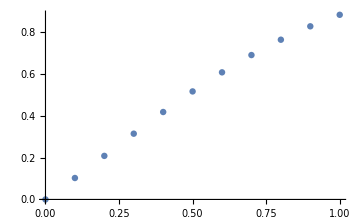

```mathematica
For[i=2, i<=(n1+1), i++,
eul1[[i,2]]=(eul1[[i-1,2]]+h1/2*(f[eul1[[i-1,1]],eul1[[i-1,2]]]+f[eul1[[i,1]],eul1[[i,2]]]));
]
grEul1=ListPlot[eul1, ImageSize->Medium]
```

{{0,0},{0.05,0.05},{0.1,0.101343},{0.15,0.153696},{0.2,0.206703},{0.25,0.259993},{0.3,0.31319},{0.35,0.365925},{0.4,0.417843},{0.45,0.468614},{0.5,0.517938},{0.55,0.565554},{0.6,0.611244},{0.65,0.654832},{0.7,0.696188},{0.75,0.735222},{0.8,0.771886},{0.85,0.806169},{0.9,0.838088},{0.95,0.867689},{1.,0.895036}}

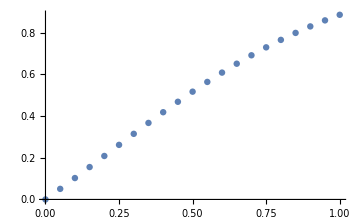

```mathematica
(*при h2*)
x=x0;
y=y0;
eul2=Table[{x,y}={x+h2,y+h2 *f[x,y]},{i,n2}];
eul2=Prepend[eul2,{x0,y0}]
For[i=2, i<=(n2+1), i++,
eul2[[i,2]]=(eul2[[i-1,2]]+h2/2*(f[eul2[[i-1,1]],eul2[[i-1,2]]]+f[eul2[[i,1]],eul2[[i,2]]]));
]
grEul2=ListPlot[eul2, ImageSize->Medium]
```

```mathematica
(*пункт б*)
```

```mathematica
(*метод Рунге-Кутта 4-го порядка*)
```

```mathematica
(*при h1*)
```

```mathematica
Clear[x,y]
```

```mathematica
sol1=List[{x0,y0}];
x=x0;y=y0;
For[k=1,k<n1+1,k++,
k1[x_,y_]:=h1*f[x,y];
k2[x_,y_]:= h1*f[x+h1/2,y+k1[x,y]/2];
k3[x_,y_]:=h1*f[x+h1/2,y+k2[x,y]/2];
k4[x_,y_]:= h1*f[x+h1,y+k3[x,y]];
x=x+h1;y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol1=Append[sol1,{x,y}]
]
```

```mathematica
sol1
```

{{0,0},{0.1,0.108477},{0.2,0.219822},{0.3,0.330773},{0.4,0.43822},{0.5,0.539513},{0.6,0.632671},{0.7,0.716461},{0.8,0.790352},{0.9,0.85439},{1.,0.909037}}

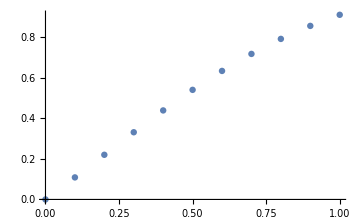

```mathematica
grSol1=ListPlot[sol1, ImageSize->Medium]
```

```mathematica
(*при h2*)
```

```mathematica
Clear[x,y]
```

```mathematica
x=x0;y=y0;
sol2=List[{x0,y0}];
For[k=1,k<n2+1,k++,
k1[x_,y_]:=h2*f[x,y];
k2[x_,y_]:= h2*f[x+h2/2,y+k1[x,y]/2];
k3[x_,y_]:=h2*f[x+h2/2,y+k2[x,y]/2];
k4[x_,y_]:= h2*f[x+h2,y+k3[x,y]];
x=x+h1;y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol2=Append[sol2,{x,y}]
]
sol2
```

{{0,0},{0.1,0.0536802},{0.2,0.109939},{0.3,0.16829},{0.4,0.228183},{0.5,0.289018},{0.6,0.350161},{0.7,0.410975},{0.8,0.47083},{0.9,0.529131},{1.,0.585328},{1.1,0.638937},{1.2,0.689544},{1.3,0.73681},{1.4,0.780476},{1.5,0.820359},{1.6,0.856344},{1.7,0.888382},{1.8,0.916479},{1.9,0.940687},{2.,0.961097}}

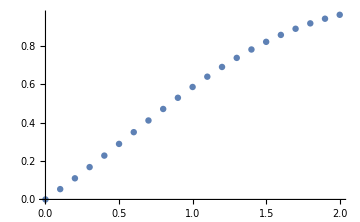

```mathematica
grSol2=ListPlot[sol2, ImageSize->Medium]
```

```mathematica
(*пункт в*)
```

```mathematica
(*используя встроенные функции DSolve и NDSolve*)
```

```mathematica
Clear[x,y]
sol1=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x]
```

{{y[x]→((0.4+0. ⅈ) ((1.+0. ⅈ) MathieuCPrime[-5.,1.5,1/2 (-π/2+x)]-(0.+0.971898 ⅈ) MathieuSPrime[-5.,1.5,1/2 (-π/2+x)]))/((1.+0. ⅈ) MathieuC[-5.,1.5,1/2 (-π/2+x)]-(0.+0.971898 ⅈ) MathieuS[-5.,1.5,1/2 (-π/2+x)])}}

```mathematica
sol2=NDSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],{x,a,b}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
y1[x_]=y[x]/.Flatten[sol1]
```

((0.4+0. ⅈ) ((1.+0. ⅈ) MathieuCPrime[-5.,1.5,1/2 (-π/2+x)]-(0.+0.971898 ⅈ) MathieuSPrime[-5.,1.5,1/2 (-π/2+x)]))/((1.+0. ⅈ) MathieuC[-5.,1.5,1/2 (-π/2+x)]-(0.+0.971898 ⅈ) MathieuS[-5.,1.5,1/2 (-π/2+x)])

```mathematica
y2[x_]=y[x]/.Flatten[sol2]
```

InterpolatingFunction[…][x]

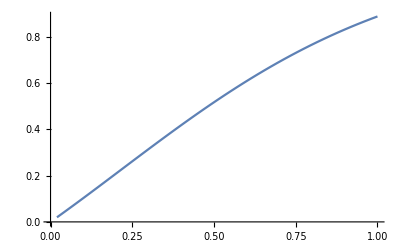

```mathematica
grDSolve=Plot[y1[x],{x,a,b}]
```

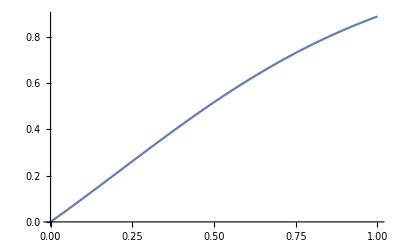

```mathematica
grNDSolve=Plot[y2[x],{x,a,b}]
```

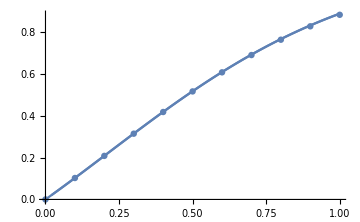

```mathematica
Show[grEul1,grNDSolve,grDSolve]
```

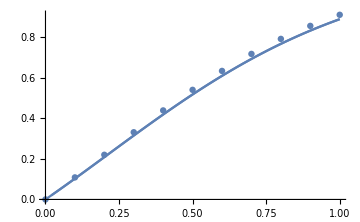

```mathematica
Show[grSol1,grNDSolve,grDSolve]
```

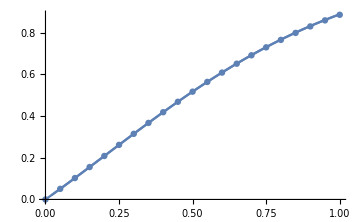

```mathematica
Show[grEul2,grNDSolve,grDSolve]
```

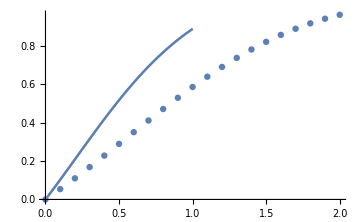

```mathematica
Show[grSol2,grNDSolve,grDSolve]
```

```mathematica
(*Задание 2*)
```

```mathematica
Clear[x,y,g,z,f,x0,y0,eul1,eul2,sol1,sol2]
```

```mathematica
f[x_,y_,z_]=2y+z+3 ⅇ^-x;
g[x_,y_,z_]=y-2z+4 ⅇ^-x;
x0=0;
y0=1;
z0=2;
a=0;
b=1;
h1=0.1;
h2=0.05;
n1=Floor[(b-a)/h1];
n2=Floor[(b-a)/h2];
```

```mathematica
(*пункт а*)
(*метод Эйлера-Коши*)
(*при h1*)
x=x0;
y=y0;
z=z0;
eul1=Table[{x,y,z}={x+h1,y+h1*f[x,y,z],z+h1*g[x,y,z]},{i,n1}]
```

{{0.1,1.7,2.1},{0.2,2.52145,2.21193},{0.3,3.49255,2.34919},{0.4,4.64823,2.52493},{0.5,6.03146,2.7529},{0.6,7.69501,3.04808},{0.7,9.70346,3.42749},{0.8,12.1359,3.91097},{0.9,15.0889,4.52209},{1.,18.6809,5.2892}}

```mathematica
eul1=Prepend[eul1,{x0,y0,z0}]
```

{{0,1,2},{0.1,1.7,2.1},{0.2,2.52145,2.21193},{0.3,3.49255,2.34919},{0.4,4.64823,2.52493},{0.5,6.03146,2.7529},{0.6,7.69501,3.04808},{0.7,9.70346,3.42749},{0.8,12.1359,3.91097},{0.9,15.0889,4.52209},{1.,18.6809,5.2892}}

```mathematica
ftable=Table[{x,y}={eul1[[i,1]],eul1[[i,2]]},{i,n1}]
```

{{0,1},{0.1,1.7},{0.2,2.52145},{0.3,3.49255},{0.4,4.64823},{0.5,6.03146},{0.6,7.69501},{0.7,9.70346},{0.8,12.1359},{0.9,15.0889}}

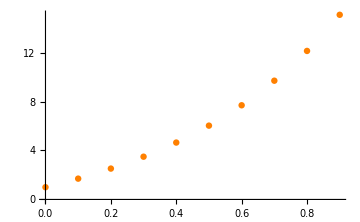

```mathematica
grEul1=ListPlot[ftable, ImageSize->Medium,PlotStyle->Orange]
```

```mathematica
ztable=Table[{x,z}={eul1[[i,1]],eul1[[i,3]]},{i,n1}]
```

{{0,2},{0.1,2.1},{0.2,2.21193},{0.3,2.34919},{0.4,2.52493},{0.5,2.7529},{0.6,3.04808},{0.7,3.42749},{0.8,3.91097},{0.9,4.52209}}

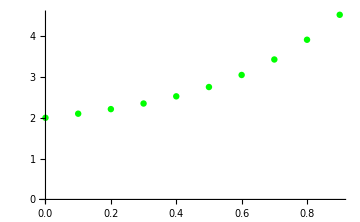

```mathematica
grEul2=ListPlot[ztable,ImageSize->Medium,PlotStyle->Green]
```

```mathematica
(*при h2*)
Clear[x,y,z]
```

```mathematica
x=x0;
y=y0;
z=z0;
```

```mathematica
eul2=Table[{x,y,z}={x+h2,y+h2*f[x,y,z],z+h2*g[x,y,z]},{i,n2}]
```

{{0.05,1.35,2.05},{0.1,1.73018,2.10275},{0.15,2.14407,2.15995},{0.2,2.59558,2.2233},{0.25,3.08911,2.29449},{0.3,3.62956,2.37526},{0.35,4.22241,2.46738},{0.4,4.87372,2.5727},{0.45,5.59027,2.69318},{0.5,6.3796,2.8309},{0.55,7.25009,2.98809},{0.6,8.21104,3.16718},{0.65,9.27283,3.37078},{0.7,10.447,3.60175},{0.75,11.7462,3.86324},{0.8,13.1849,4.1587},{0.85,14.7787,4.49194},{0.9,16.5453,4.86716},{0.95,18.5041,5.28902},{1.,20.677,5.76268}}

```mathematica
eul2=Prepend[eul2,{x0,y0,z0}]
```

{{0,1,2},{0.05,1.35,2.05},{0.1,1.73018,2.10275},{0.15,2.14407,2.15995},{0.2,2.59558,2.2233},{0.25,3.08911,2.29449},{0.3,3.62956,2.37526},{0.35,4.22241,2.46738},{0.4,4.87372,2.5727},{0.45,5.59027,2.69318},{0.5,6.3796,2.8309},{0.55,7.25009,2.98809},{0.6,8.21104,3.16718},{0.65,9.27283,3.37078},{0.7,10.447,3.60175},{0.75,11.7462,3.86324},{0.8,13.1849,4.1587},{0.85,14.7787,4.49194},{0.9,16.5453,4.86716},{0.95,18.5041,5.28902},{1.,20.677,5.76268}}

```mathematica
ftable=Table[{x,y}={eul2[[i,1]],eul2[[i,2]]},{i,n2}]
```

{{0,1},{0.05,1.35},{0.1,1.73018},{0.15,2.14407},{0.2,2.59558},{0.25,3.08911},{0.3,3.62956},{0.35,4.22241},{0.4,4.87372},{0.45,5.59027},{0.5,6.3796},{0.55,7.25009},{0.6,8.21104},{0.65,9.27283},{0.7,10.447},{0.75,11.7462},{0.8,13.1849},{0.85,14.7787},{0.9,16.5453},{0.95,18.5041}}

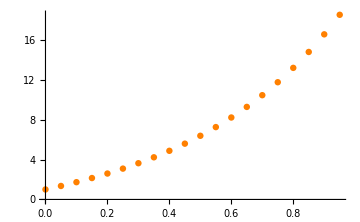

```mathematica
grEul3=ListPlot[ftable, ImageSize->Medium,PlotStyle->Orange]
```

```mathematica
ztable=Table[{x,z}={eul2[[i,1]],eul2[[i,3]]},{i,n2}]
```

{{0,2},{0.05,2.05},{0.1,2.10275},{0.15,2.15995},{0.2,2.2233},{0.25,2.29449},{0.3,2.37526},{0.35,2.46738},{0.4,2.5727},{0.45,2.69318},{0.5,2.8309},{0.55,2.98809},{0.6,3.16718},{0.65,3.37078},{0.7,3.60175},{0.75,3.86324},{0.8,4.1587},{0.85,4.49194},{0.9,4.86716},{0.95,5.28902}}

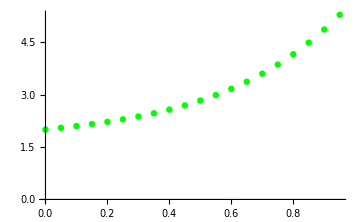

```mathematica
grEul4=ListPlot[ztable,ImageSize->Medium,PlotStyle->Green]
```

```mathematica
(*пункт б*)
```

```mathematica
(*метод Рунге-Кутта 4-го порядка*)
```

```mathematica
(*при h1*)
```

```mathematica
Clear[x,y,z]
```

```mathematica
x=x0;y=y0;z=z0;
```

```mathematica
Clear[sol1]
```

```mathematica
sol1=List[{x0,y0,z0}];
```

```mathematica
For[k=1, k<n1+1,k++,
k1[x_,y_,z_]:=h1*f[x,y,z];
r1[x_,y_,z_]:=h1*g[x,y,z];
k2[x_,y_,z_]:=h1*f[x+h1/2,y+k1[x,y,z]/2, z+r1[x,y,z]/2];
r2[x_,y_,z_]:=h1*g[x+h1/2,y+k1[x,y,z]/2, z+r1[x,y,z]/2];
k3[x_,y_,z_]:=h1*f[x+h1/2,y+k2[x,y,z]/2, z+r2[x,y,z]/2];
r3[x_,y_,z_]:=h1*g[x+h1/2,y+k2[x,y,z]/2, z+r2[x,y,z]/2];
k4[x_,y_,z_]:=h1*f[x+h1/2,y+k3[x,y,z]/2, z+r3[x,y,z]/2];
r4[x_,y_,z_]:=h1*g[x+h1/2,y+k3[x,y,z]/2, z+r3[x,y,z]/2];
x=x+h1;y=y+(k1[x,y,z]+2*k2[x,y,z]+2*k3[x,y,z]+k4[x,y,z])/6;
z=z+(r1[x,y,z]+2*r2[x,y,z]+2*r3[x,y,z]+r4[x,y,z])/6;
sol1=Append[sol1, {x,y,z}]
];
```

```mathematica
sol1
```

{{0,1,2},{0.1,1.72217,2.14367},{0.2,2.59077,2.31732},{0.3,3.64408,2.53713},{0.4,4.9302,2.82091},{0.5,6.5095,3.18908},{0.6,8.45761,3.66576},{0.7,10.8692,4.28001},{0.8,13.8627,5.0674},{0.9,17.5862,6.07181},{1.,22.2252,7.34769}}

```mathematica
ftable=Table[{x,y}={sol1[[i,1]],sol1[[i,2]]},{i,n1}]
```

{{0,1},{0.1,1.72217},{0.2,2.59077},{0.3,3.64408},{0.4,4.9302},{0.5,6.5095},{0.6,8.45761},{0.7,10.8692},{0.8,13.8627},{0.9,17.5862}}

```mathematica
ztable=Table[{x,z}={sol1[[i,1]],sol1[[i,3]]},{i,n1}]
```

{{0,2},{0.1,2.14367},{0.2,2.31732},{0.3,2.53713},{0.4,2.82091},{0.5,3.18908},{0.6,3.66576},{0.7,4.28001},{0.8,5.0674},{0.9,6.07181}}

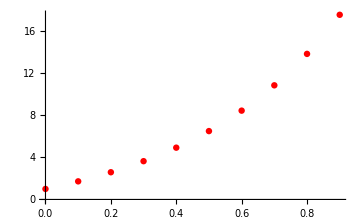

```mathematica
grSol1=ListPlot[ftable,ImageSize->Medium,PlotStyle->Red]
```

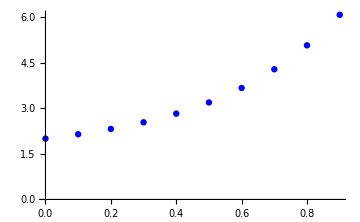

```mathematica
grSol2=ListPlot[ztable,ImageSize->Medium,PlotStyle->Blue]
```

```mathematica
(*при h2*)
```

```mathematica
Clear[x,y,g,z,f,x0,y0,sol1,sol2]
```

```mathematica
f[x_,y_,z_]=2y+z+3 ⅇ^-x;
g[x_,y_,z_]=y-2z+4 ⅇ^-x;
x0=0;
y0=1;
z0=2;
a=0;
b=1;
h1=0.1;
h2=0.05;
n1=Floor[(b-a)/h1];
n2=Floor[(b-a)/h2];
```

```mathematica
x=x0;y=y0;z=z0;
```

```mathematica
sol2=List[{x0,y0,z0}];
```

```mathematica
For[k=1, k<n2+1,k++,
k1[x_,y_,z_]:=h2*f[x,y,z];
r1[x_,y_,z_]:=h2*g[x,y,z];
k2[x_,y_,z_]:=h2*f[x+h1/2,y+k1[x,y,z]/2, z+r1[x,y,z]/2];
r2[x_,y_,z_]:=h2*g[x+h1/2,y+k1[x,y,z]/2, z+r1[x,y,z]/2];
k3[x_,y_,z_]:=h2*f[x+h1/2,y+k2[x,y,z]/2, z+r2[x,y,z]/2];
r3[x_,y_,z_]:=h2*g[x+h1/2,y+k2[x,y,z]/2, z+r2[x,y,z]/2];
k4[x_,y_,z_]:=h2*f[x+h1/2,y+k3[x,y,z]/2, z+r3[x,y,z]/2];
r4[x_,y_,z_]:=h2*g[x+h1/2,y+k3[x,y,z]/2, z+r3[x,y,z]/2];
x=x+h2;
y=y+(k1[x,y,z]+2*k2[x,y,z]+2*k3[x,y,z]+k4[x,y,z])/6;
z=z+(r1[x,y,z]+2*r2[x,y,z]+2*r3[x,y,z]+r4[x,y,z])/6;
sol2=Append[sol2, {x,y,z}]
];
sol2
```

{{0,1,2},{0.05,1.35225,2.05582},{0.1,1.73726,2.11695},{0.15,2.15909,2.18513},{0.2,2.62231,2.26219},{0.25,3.13204,2.34998},{0.3,3.69401,2.45047},{0.35,4.31465,2.56574},{0.4,5.00117,2.69802},{0.45,5.76159,2.8497},{0.5,6.60495,3.02339},{0.55,7.5413,3.22195},{0.6,8.58191,3.4485},{0.65,9.73939,3.7065},{0.7,11.0278,3.99976},{0.75,12.463,4.33252},{0.8,14.0624,4.70947},{0.85,15.8459,5.13584},{0.9,17.8355,5.61747},{0.95,20.0558,6.16084},{1.,22.5343,6.77321}}

```mathematica
ftable=Table[{x,y}={sol2[[i,1]],sol2[[i,2]]},{i,n2}]
```

{{0,1},{0.05,1.35225},{0.1,1.73726},{0.15,2.15909},{0.2,2.62231},{0.25,3.13204},{0.3,3.69401},{0.35,4.31465},{0.4,5.00117},{0.45,5.76159},{0.5,6.60495},{0.55,7.5413},{0.6,8.58191},{0.65,9.73939},{0.7,11.0278},{0.75,12.463},{0.8,14.0624},{0.85,15.8459},{0.9,17.8355},{0.95,20.0558}}

```mathematica
ztable=Table[{x,z}={sol2[[i,1]],sol2[[i,3]]},{i,n2}]
```

{{0,2},{0.05,2.05582},{0.1,2.11695},{0.15,2.18513},{0.2,2.26219},{0.25,2.34998},{0.3,2.45047},{0.35,2.56574},{0.4,2.69802},{0.45,2.8497},{0.5,3.02339},{0.55,3.22195},{0.6,3.4485},{0.65,3.7065},{0.7,3.99976},{0.75,4.33252},{0.8,4.70947},{0.85,5.13584},{0.9,5.61747},{0.95,6.16084}}

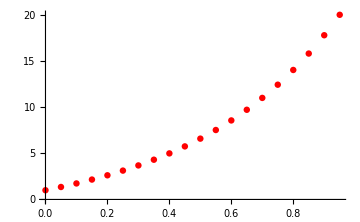

```mathematica
grSol3=ListPlot[ftable,ImageSize->Medium,PlotStyle-> Red]
```

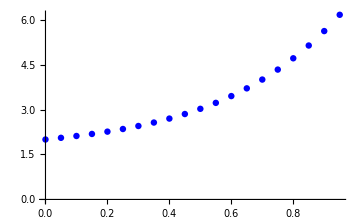

```mathematica
grSol4=ListPlot[ztable,ImageSize->Medium,PlotStyle->Blue]
```

```mathematica
(*пункт в*)
```

```mathematica
(*используя встроенные функции DSolve и NDSolve*)
```

```mathematica
Clear[x,y,z]
```

```mathematica
sol=DSolve[{y'[x]==f[x,y[x],z[x]],z'[x]==g[x,y[x],z[x]],y[0]==0.5,z[0]==2},{y,z},{x,a,b}]
```

{{y→Function[{x},-1.75 ⅇ^-x+0.174671 ⅇ^(-√5 x)+2.07533 ⅇ^(√5 x)],z→Function[{x},2.25 ⅇ^-x-0.739919 ⅇ^(-√5 x)+0.489919 ⅇ^(√5 x)]}}

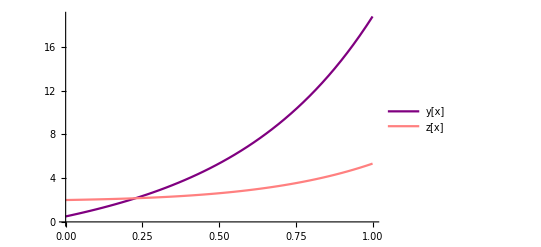

```mathematica
grDSolve=Plot[Evaluate[{y[x],z[x]}/.sol],{x,a,b},PlotLegends->{"y[x]","z[x]"},PlotStyle->{Purple,Pink}]
```

```mathematica
Clear[x,y,z,sol]
sol=NDSolve[{y'[x]==f[x,y[x],z[x]],z'[x]==g[x,y[x],z[x]],y[0]==0.5,z[0]==2},{y,z},{x,a,b}]
```

{{y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

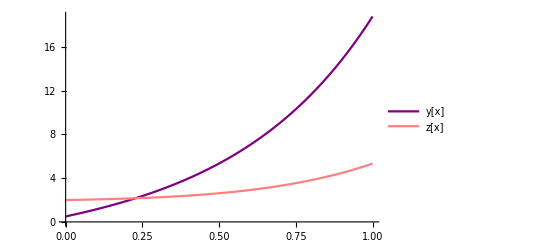

```mathematica
grNDSolve=Plot[Evaluate[{y[x],z[x]}/.sol],{x,a,b},PlotLegends->{"y[x]","z[x]"},PlotStyle->{Purple,Pink}]
```

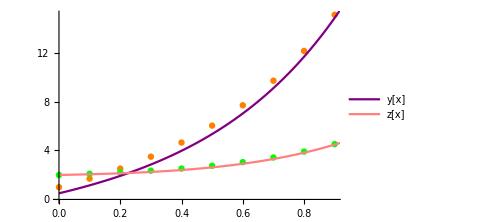

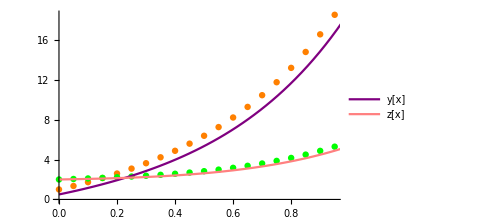

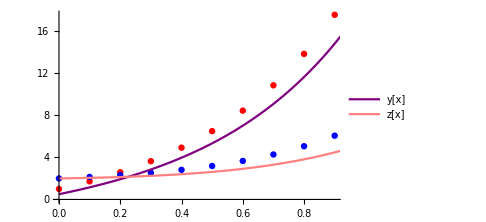

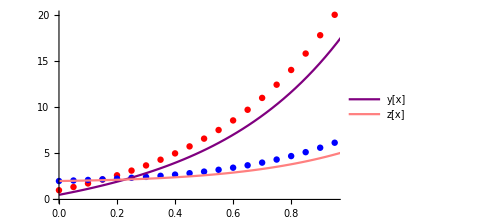

```mathematica
Show[grEul1,grEul2,grNDSolve]
Show[grEul3,grEul4,grNDSolve]
Show[grSol1,grSol2,grNDSolve]
Show[grSol3,grSol4,grNDSolve]
```